## Initialization

```mathematica
myPrint[msg_,rest_]:=Print[StringForm@@Flatten[{msg,rest}]];
g=9.81;
l=100;(*Pool length*)
h=2;(*Pool depth*)
tMax=60;

meetDist=90;
wavePeriod[a_]:=a/√((a g)/(2π)Tanh[(2π h)/a]);
travelTime[a_]:=meetDist/√((a g)/(2π)Tanh[(2π h)/a]);
hanWindow[x_,p_]:=HannWindow@((x-p/2)/p);
composeBoundary[waves_]:=Module[{periods},
periods=Array[wavePeriod[waves[[1,#]]]&,Length[waves[[1]]]];
Return[Total[Array[Sin[(2π)/periods[[#]](time-waves[[2,#]])]hanWindow[time-waves[[2,#]],1.5periods[[#]]]&,Length[waves[[1]]]]]];
];
calcLengths[meetTime_,numWaves_Integer,timeWait_]:=Module[{resLength,waitTimes,lag,idx,waveRoot},
resLength=Table[0.0,numWaves];
waitTimes=Table[0.0,numWaves];
lag=0.0;

For[idx=1,idx≤numWaves,idx++,
waveRoot=FindRoot[meetTime-lag==travelTime[x]+0.75wavePeriod[x],{x,0.001}];
resLength[[idx]]=waveRoot[[1,2]];
waitTimes[[idx]]=lag;
lag=lag+timeWait+1.5wavePeriod[resLength[[idx]]]
];

Return[{resLength,waitTimes}];
];

(*
True -> use number of intervals, compute the step;
False -> use the step size, compute number of intervals
*)
useNIntervals=False;
If[useNIntervals,(
xIntervals=250;
zIntervals=30;
),(*else*) (
stepTarget=0.25;
xIntervals=Ceiling[l/stepTarget];
zIntervals=Ceiling[h/stepTarget];
)]
n=xIntervals+1;
m=zIntervals+1;
numNodes=n*m;
Δx=N[l/xIntervals];
Δz=N[h/zIntervals];
τ=Min[Δx,Δz];
(*τ=0.01;*)
tIntervals=Ceiling[tMax/τ];
t=tIntervals+1;
τ=N[tMax/tIntervals];
xCoord=Table[Δx(i-1),{i,1,n}];
zCoord=Table[Δz(i-1),{i,1,m}];
tCoord=Table[τ(i-1),{i,1,t}];
index=Table[1+(i-1)m+(j-1),{i,1,n},{j,1,m}];
myPrint["Number of points X,Z,T = (``, ``, ``)",{n,m,t}];
myPrint["Δx,Δz,τ = (``, ``, ``)",{Δx,Δz,τ}];

(*Surface variable*)
hInitial[x_]:=1/((0.2)2π)Exp[-0.5((x/l-0.3)/0.05)^2];
hVal=NIntegrate[hInitial[x],{x,0,l}]/l;
hNorm[x_]:=hInitial[x]-hVal;
hNorm[x_]:=0;
(*Right boundary movement*)
rightSpeed=5;
rightPeriod=8;
rightBlend=2rightPeriod;
rightDisplace[t_]:=-0.1Which[t*rightSpeed<1,3(t*rightSpeed)^2-2(t*rightSpeed)^3,t*rightSpeed<2,(t*rightSpeed-2)^2(2t*rightSpeed-1),True,0];
rightDisplace[t_]:=Which[t<rightBlend,-1.5Sin[(2π)/rightPeriod t](3(t/rightBlend)^2-2(t/rightBlend)^3),t<tMax/2-rightBlend,-1.5Sin[(2π)/rightPeriod t],t<tMax/2,-1.5Sin[(2π)/rightPeriod t](3(1-(t-(tMax/2-rightBlend))/rightBlend)^2-2((1-(t-(tMax/2-rightBlend))/rightBlend))^3),True,0];

pistonWave=calcLengths[34.0(*meetTime*),3(*numWaves*),1.0(*Wait time*)]
rightDisplace[t_]:=-0.5composeBoundary[pistonWave]/.{time->t};
rightVelFunc=Simplify[D[rightDisplace[q],q]];
rightVel[t_]:=rightVelFunc/.{q->t}

(*Matrix helper*)
centerIdx=1;
leftIdx=2;
rightIdx=3;
bottomIdx=4;
topIdx=5;
Plot[rightDisplace[x],{x,0,tMax},PlotRange->All,AxesLabel->{"t","P(t)"}]
Plot[rightVel[x],{x,0,tMax},PlotRange->All,AxesLabel->{"t","P'(t)"}]
```

Number of points X,Z,T = (401, 9, 241)

Δx,Δz,τ = (0.25, 0.25, 0.25)

{{4.92299,6.55367,11.1847},{0.,3.67975,7.82007}}

## Function definitions

```mathematica
buildMatrix[tIndex_Integer]:=Module[{i,j,result,center,left,right,bottom,top,mainIdx,tg},
(*Sparce matrix. We only need the center and 4 neighbors from each cell*)
result=Table[0.0,numNodes,5];

(*Add contributions to nodes below the free surface*)
For[j=1,j≤m-1,j++,
For[i=1,i≤n,i++,
center=-2.0(Δx/Δz)-2.0(Δz/Δx);
left=right=Δz/Δx;
top=bottom=Δx/Δz;
If[i==1,
(*Left boundary*)
right+=left;
left=0;
];
If[i==n,
(*Right boundary*)
left+=right;
right=0;
];
If[j==1,
(*Bottom boundary*)
top+=bottom;
bottom=0;
];

mainIdx=index[[i,j]];
result[[mainIdx,centerIdx]]=center;
result[[mainIdx,leftIdx]]=left;
result[[mainIdx,rightIdx]]=right;
result[[mainIdx,bottomIdx]]=bottom;
result[[mainIdx,topIdx]]=top;
];
];

(*Add contributions to nodes on the free surface*)
tg=τ^2 g;
For[i=1,i≤n,i++,
center=-(4+tg/Δz+(tg Δz)/Δx^2);
left=right=(tg Δz)/(2 Δx^2);
bottom=tg/Δz;
top=0;
If[i==1,
(*Left boundary*)
right+=left;
left=0;
];
If[i==n,
(*Right boundary*)
left+=right;
right=0;
];

mainIdx=index[[i,m]];
result[[mainIdx,centerIdx]]=center;
result[[mainIdx,leftIdx]]=left;
result[[mainIdx,rightIdx]]=right;
result[[mainIdx,bottomIdx]]=bottom;
result[[mainIdx,topIdx]]=top;
];

Return[result];
];
buildRightSide[tIndex_Integer,ϕ_,hi_]:=Module[{result,i,tg,mainIdx},
result=Table[0.0,numNodes];
(*Contributions from nodes on the right boundary. Skip the free surface node*)
For[i=1,i<m,i++,
result[[index[[n,i]]]]=-2Δz rightVel[tCoord[[tIndex]]];
];

(*Contributions from nodes on the free surface*)
tg=τ g;
For[i=1,i≤n,i++,
mainIdx=index[[i,m]];
result[[mainIdx]]=-4ϕ[[mainIdx]]+τ(4 g hi[[i]]
+tg/Δz(ϕ[[mainIdx]]-ϕ[[index[[i,m-1]]]])
+(tg Δz)/Δx^2 ϕ[[mainIdx]]
-(tg Δz)/(2 Δx^2)(ϕ[[index[[If[i>1,i-1,i+1],m]]]]+ϕ[[index[[If[i<n,i+1,i-1],m]]]])
);
(*Right boundary contribution*)
If[i==n,result[[mainIdx]]+=-(τ^2 g Δz)/Δx(rightVel[tCoord[[tIndex+1]]]+rightVel[tCoord[[tIndex]]])];
];
Return[result];
];
(*Find the solution of X's of the given tridiagonal block matrix
@param matrix A table of n*m vectors of 5 elements. These are all the non-zero elements in the actual matrix.
@param rhx A vector of n*m elements. This is the right hand side of the linear system.
@param n The number of blocks.
@param m The size of each block. They are square.
The time complexity of the algorithm is O(n*m^3). For better performance pick m<n.
*)
solveBlockTridiag[matrix_,rhs_,n_,m_]:=Module[{w,f,k,i,a,b,result},
w=Table[0,n];
f=Table[0,n];
k=Table[0,n];
w[[1]]=Inverse[
SparseArray[{
Band[{1,1}]->matrix[[1;;m,centerIdx]],
Band[{2,1}]->matrix[[2;;m,bottomIdx]],
Band[{1,2}]->matrix[[1;;m-1,topIdx]]},{m,m}]];
f[[1]]=w[[1]].rhs[[1;;m]];
k[[1]]=w[[1]].SparseArray[Band[{1,1}]->matrix[[1;;m,rightIdx]],{m,m}];

For[i=2,i≤n-1,i++,
a=SparseArray[Band[{1,1}]->matrix[[1+(i-1)m;;i m,leftIdx]],{m,m}];
b=SparseArray[Band[{1,1}]->matrix[[1+(i-1)m;;i m,rightIdx]],{m,m}];
w[[i]]=Inverse[
SparseArray[{
Band[{1,1}]->matrix[[1+(i-1)m;;i m,centerIdx]],
Band[{2,1}]->matrix[[2+(i-1)m;;i m,bottomIdx]],
Band[{1,2}]->matrix[[1+(i-1)m;;i m-1,topIdx]]},{m,m}]
-a.k[[i-1]]];
f[[i]]=w[[i]].(rhs[[1+(i-1)m;;i m]]-a.f[[i-1]]);
k[[i]]=w[[i]].b;
];

result=Table[0,n m];
a=SparseArray[Band[{1,1}]->matrix[[1+(n-1) m;;n m,leftIdx]],{m,m}];
w[[n]]=Inverse[
SparseArray[{
Band[{1,1}]->matrix[[1+(n-1) m;;n m,centerIdx]],
Band[{2,1}]->matrix[[2+(n-1) m;;n m,bottomIdx]],
Band[{1,2}]->matrix[[1+(n-1) m;;n m-1,topIdx]]},{m,m}]
-a.k[[n-1]]];
result[[1+(n-1) m;;n m]]=w[[n]].(rhs[[1+(n-1) m;;n m]]-a.f[[n-1]]);
For[i=n-1,i≥1,i--,
result[[1+(i-1) m;;i m]]=f[[i]]-k[[i]].result[[1+i m;;(i+1) m]];
];

Return[result];
];
buildInterpolation[hi_,xs_,ts_]:=Interpolation[Flatten[Table[{{xs[[i]],ts[[j]]},hi[[j,i]]},{j,1,t},{i,1,n}],1],InterpolationOrder->1];
```

## Solve linear system using block tri-diagonal solver

```mathematica
solutionH=None;
solutionF=Table[0,t];
Module[{mat,rhs,i,j,k,ϕ,hi,kCurr,kPrev,elapseT,hRem,mRem,sRem,tTotal,tRem},Monitor[
hi=Table[0.0,{i,1,t},{j,1,n}];
For[i=1,i≤n,i++,hi[[1,i]]=hNorm[xCoord[[i]]]];
ϕ=Table[0.0,2,numNodes];
solutionF[[1]]=ϕ[[1]];

tTotal=0;
hRem=99;
mRem=99;
sRem=99;
For[k=2,k≤t,k++,
kCurr=1+Mod[k,2];
kPrev=1+Mod[k-1,2];
elapseT=AbsoluteTiming[
mat=buildMatrix[k-1];
rhs=buildRightSide[k-1,ϕ[[kPrev]],hi[[k-1]]];
ϕ[[kCurr]]=solveBlockTridiag[mat,rhs,n,m];
solutionF[[k]]=ϕ[[kCurr]];

(*Update the free surface height*)
For[i=1,i≤n,i++,
hi[[k,i]]=-(2/(τ g)(ϕ[[kCurr,index[[i,m]]]]-ϕ[[kPrev,index[[i,m]]]])+hi[[k-1,i]]);
];
][[1]];
tTotal+=elapseT;
tRem=tTotal(t-1)/(k-1)-tTotal;
hRem=Floor[tRem/3600];
mRem=Floor[Mod[tRem,3600]/60];
sRem=Floor[Mod[tRem,60]];
];
myPrint["Done!",{}];
solutionH=hi;

,Row[{ProgressIndicator[(k-1)/(t-1)],StringForm["``/``, Time remaining: ``h, ``m, ``s",(k-1),(t-1),hRem,mRem,sRem]}," "]];
];
(*ListPlot3D[solutionH,PlotRange->{-1,1},DataRange->{{0,l},{0,tMax}}]*)
```

Done!

```mathematica
finiteSol=buildInterpolation[solutionH,xCoord,tCoord];
nF=40;(*Number of fourier coefficients*)
ks=Table[(i π)/l,{x,0,nF}];
coeff=Table[2/l NIntegrate[hInitial[x]Cos[(i π)/l x],{x,0,l}],{i,1,nF}];
omega=Table[√((i π)/l g Tanh[(i π)/l h]),{i,1,nF}];
basis=Table[Cos[(i π)/l x]Cos[omega[[i]] time],{i,1,nF}];
Manipulate[
Show[
(*Plot[hNorm[x],{x,0,l},PlotRange->{-1,1},PlotStyle->Red],*)
Plot[h+finiteSol[x,t],{x,0,l},PlotRange->{-0.5,2h+0.5},PlotStyle->Red]
(*,Plot[basis.coeff/.{time->t},{x,0,l},PlotRange->{-1,1}]*)
]
,{t,0,tMax,AnimationRate->1,Appearance->"Open"}]
```

```mathematica
√(34.3 g/(2π)Tanh[2π h/34.3])
```

4.33438

```mathematica
N[2 π/rightPeriod]
```

0.785398

```mathematica
root=FindRoot[rightPeriod==x/(√((x g)/(2π)Tanh[2 π/x h])),{x,2}]
```

{x→34.6915}

```mathematica
√(2π g/x Tanh[2π h/x])/.root
```

0.785398

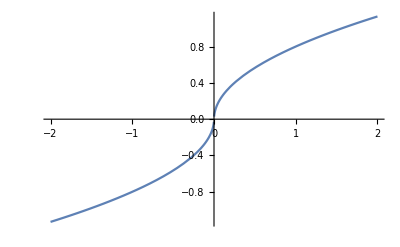

```mathematica
Plot[x/(√((x g)/(2π)Tanh[2 π/x h])),{x,-2,2}]
```

```mathematica
=90;
windTime1[a_]:=a/√((a g)/(2π)Tanh[(2π h)/a]);
windTime2[a_]:=a/√((a g)/(2π)Tanh[(2π h)/a]);
windTime3[a_]:=a/√((a g)/(2π)Tanh[(2π h)/a]);
travelTime1[a_]:=windTime1[a]+meetDist/√((a g)/(2π)Tanh[(2π h)/a]);
travelTime2[a_]:=windTime2[a]+meetDist/√((a g)/(2π)Tanh[(2π h)/a]);
travelTime3[a_]:=windTime3[a]+meetDist/√((a g)/(2π)Tanh[(2π h)/a]);
Manipulate[
Plot[{
travelTime1[x],
travelTime2[x]+t2+windTime1[a1],
travelTime3[x]+t2+t3+windTime1[a1]+windTime2[a2]
},{x,0,50},PlotLegends->"Expressions",PlotRange->{{0,60},{0,100}}]
,{{a1,20},0,100},{{a2,20},0,100},{t2,0,100},{t3,0,100}]
```

```mathematica
Manipulate[
Show[
(*Plot[hNorm[x],{x,0,l},PlotRange->{-1,1},PlotStyle->Red],*)
Plot[finiteSol[x,t],{x,0,l},PlotRange->{-2h,5h},PlotStyle->Red]
(*,Plot[basis.coeff/.{time->t},{x,0,l},PlotRange->{-1,1}]*)
]
,{t,0,4π,AnimationRate->1/50,Appearance->"Open"}]
```

```mathematica
DensityPlot[basis.coeff,{x,0,l},{time,0,10},PlotRange->Full,MaxRecursion->4,FrameLabel->{"x","t"},PlotLegends->BarLegend[{Automatic,{-0.2,0.6}}],ColorFunctionScaling->False,ColorFunction->(ColorData["M10DefaultDensityGradient","ColorFunction"][Rescale[#,{-0.2,0.6}]]&)]
```

```mathematica
errorFunc=buildInterpolation[Table[(basis.coeff/.{x->xCoord[[xx]],time->tCoord[[tt]]})-solutionH[[tt,xx]],{tt,Length[tCoord]},{xx,Length[xCoord]}],xCoord,tCoord];
```

```mathematica
DensityPlot[Abs[errorFunc[x,time]],{x,0,l},{time,0,10},PlotRange->Full,MaxRecursion->4,FrameLabel->{"x","t"},PlotLegends->BarLegend[{Automatic,{0,0.1}}],ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow","ColorFunction"][Rescale[#,{0,0.1}]]&)]
```

```mathematica
DensityPlot[100Abs[basis.coeff-finiteSol[t1,t2]/.{t1->x,t2->time}]/(basis.coeff+10^-3),{x,0,l},{time,0,10},PlotRange->Full,MaxRecursion->4,FrameLabel->{"x","t"},PlotLegends->BarLegend[{Automatic,{0,100}}],ColorFunctionScaling->False,ColorFunction->(ColorData["BlueGreenYellow","ColorFunction"][Rescale[#,{0,100}]]&)]
```

```mathematica
basisH=Table[Cos[ks[[i]]x]Cos[omega[[i]] time],{i,1,nF}];
exactH=Table[basisH.coeff/.{time->tCoord[[kk]],x->xCoord[[i]]},{kk,1,t},{i,1,n}];
```

```mathematica
errorsH=Array[exactH[[#]]-solutionH[[#]]&,Length[solutionH]];
```

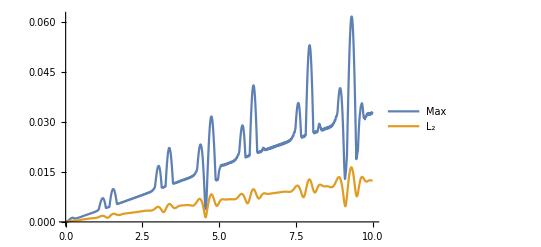

```mathematica
ListLinePlot[{Max[Abs[#]]&/@errorsH,Norm[#]/Sqrt[Length[#]]&/@errorsH},DataRange->{0,tMax},PlotLegends->{"Max","L_2"}]
```

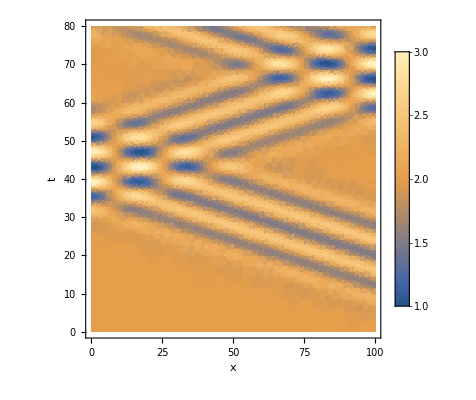

```mathematica
DensityPlot[h+finiteSol[x,time],{x,0,l},{time,0,tMax},PlotRange->Full,MaxRecursion->15,FrameLabel->{"x","t"},PlotLegends->BarLegend[{Automatic,{1,3}}],ColorFunctionScaling->False,ColorFunction->(ColorData["M10DefaultDensityGradient","ColorFunction"][Rescale[#,{1,3}]]&)]
```